```mathematica
seqList100 = {{1,1},{2,3.90/2.26},{3,5.30/2.26},{4,6.17/2.26},{5,6.99/2.26},{6,7.53/2.26},{7,8.25/2.26},{8,8.30/2.26},{12,7.16/2.26},{16,7.57/2.26},{24,6.67/2.26},{32,6.69/2.26}};
threadList100 ={{1,1},{2,3.90/2.13},{3,5.30/2.13},{4,6.17/2.13},{5,6.99/2.13},{6,7.53/2.13},{7,8.25/2.13},{8,8.30/2.13},{12,7.16/2.13},{16,7.57/2.13},{24,6.67/2.13},{32,6.69/2.13}};
```

```mathematica
seqList1000 = {{1,1},{2,3.57/1.88},{3,4.84/1.88},{4,6.53/1.88},{5,7.67/1.88},{6,8.66/1.88},{7,9.42/1.88},{8,9.57/1.88},{12,18.20/1.88},{16,24.50/1.88},{24,33.06/1.88},{32,42.14/1.88}};
threadList1000 ={{1,1},{2,3.57/1.79},{3,4.84/1.79},{4,6.53/1.79},{5,7.67/1.79},{6,8.66/1.79},{7,9.42/1.79},{8,9.57/1.79},{12,18.20/1.79},{16,24.50/1.79},{24,33.06/1.79},{32,42.14/1.79}};
```

```mathematica
seqList5000 = {{1,1},{2,3.608/1.925},{3,5.26/1.925},{4,6.64/1.925},{5,7.77/1.925},{6,8.32/1.925},{7,8.97/1.925},{8,8.74/1.925},{12,12.71/1.925},{16,17.22/1.925},{24,25.08/1.925},{32,33.42/1.925}};
threadList5000 ={{1,1},{2,3.608/1.815},{3,5.26/1.815},{4,6.64/1.815},{5,7.77/1.815},{6,8.32/1.815},{7,8.97/1.815},{8,8.74/1.815},{12,12.71/1.815},{16,17.22/1.815},{24,25.08/1.815},{32,33.42/1.815}};
```

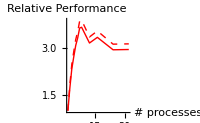

```mathematica
ListPlot[{seqList100,threadList100},Joined->True,PlotStyle->{{Red,Thick},{Red,Dashed,Thick}},PlotRange->All,AxesLabel->{"# processes","Relative Performance"},ImageSize->200,AxesOrigin->{0,0}]
```

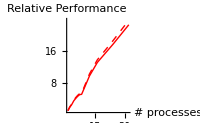

```mathematica
ListPlot[{seqList1000,threadList1000},Joined->True,PlotStyle->{{Red,Thick},{Red,Dashed,Thick}},PlotRange->All,AxesLabel->{"# processes","Relative Performance"},ImageSize->200,AxesOrigin->{0,0}]
```

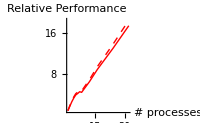

```mathematica
ListPlot[{seqList5000,threadList5000},Joined->True,PlotStyle->{{Red,Thick},{Red,Dashed,Thick}},PlotRange->All,AxesLabel->{"# processes","Relative Performance"},ImageSize->200,AxesOrigin->{0,0}]
```

```mathematica
OriginalList={{1,6.09 10^-6},{10,7.41 10^-6},{100,1.28 10^-5},{1000,9.81 10^-6},{10000,3 10^-4},{100000,2.21 10^-4},{1000000,1.07 10^-3},{10000000,9.82 10^-3},{100000000,9.64 10^-2}};
```

```mathematica
NaiveList={{1,3.37 10^-5},{10,4.00 10^-5},{100,4.60 10^-5},{1000,1.09 10^-4},{10000,1.34 10^-4},{100000,4.80 10^-4},{1000000,4.43 10^-3},{10000000,4.50 10^-2},{100000000,4.47 10^-1}};
```

```mathematica
CascadeList={{1,2.07 10^-5},{10,2.13 10^-5},{100,2.40 10^-5},{1000,3.39 10^-5},{10000,4.95 10^-5},{100000,2.02 10^-4},{1000000,1.37 10^-3},{10000000,1.41 10^-2},{100000000,1.41 10^-1}};
```

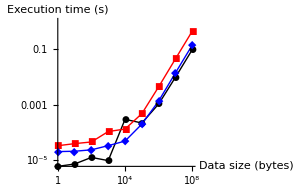

```mathematica
ListLogLogPlot[{OriginalList,NaiveList,CascadeList},Joined->True,PlotMarkers->Automatic,AxesLabel->{"Data size (bytes)","Execution time (s)"},ImageSize->300,PlotStyle->{Black,Red,Blue}]
```